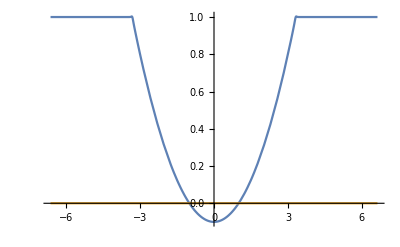

```mathematica
(*Configuration*)
a=0.1;
v=0.0000001;
n=100;

b=(1+1/a)^(-n);
Epsilon = Function[x,1+(a*(x^2-1)+ⅈ*v-1)/(1+b*x^(2n))];

X0=2*Sqrt[1/a+1];
Plot[{Re[Epsilon[x]],Im[Epsilon[x]]},{x,-X0,X0},PlotRange->Full]

χ=20;
A=1;
t=0.1;
```

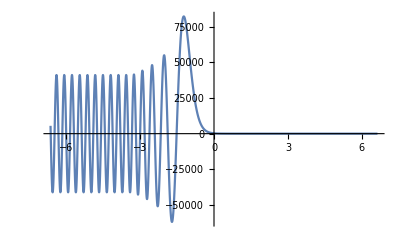

0.0000228624

```mathematica
(*TE-wave*)
ETEEquation={y''[x]+χ^2*(Epsilon[x]-Sin[teta]^2)*y[x]==0};
ETEInitials={y[X0]==A,y'[X0]==ⅈ*χ*A};

ETE=ParametricNDSolveValue[{ETEEquation,ETEInitials},y,{x,-X0,X0},{teta}];
Plot[Re[ETE[0][x]],{x,-X0,X0},PlotRange->Full]

RTE=Function[teta,Exp[2*ⅈ*χ*(-X0)]*(ⅈ*χ*ETE[teta][-X0]-ETE[teta]'[-X0])/(ⅈ*χ*ETE[teta][-X0]+ETE[teta]'[-X0])];
TTE=Function[teta,ETE[teta][X0]*Exp[-ⅈ*χ*(X0)]*(Exp[ⅈ*χ*(-X0)]+RTE[teta]*Exp[-ⅈ*χ*(-X0)])/ETE[teta][-X0]];

TEDissipation =Function[teta,1 - Abs[RTE[teta]]^2-Abs[TTE[teta]]^2];
(*Plot[TEDissipation[x],{x,-π/2,π/2},PlotRange->Full]*)
TEDissipation[t]
```

NDSolveValue::precw: The precision of the differential equation ({400 (0.9900332889206208`  + Power[« 2 »] Plus[« 2 »]) y[x] - (0.2` x Power[« 2 »] - 1.4513143180296405`*^-102 Power[« 2 »] Power[« 2 »] Plus[« 2 »]) SuperscriptBox[{}{}{}{}) is less than WorkingPrecision (30.).

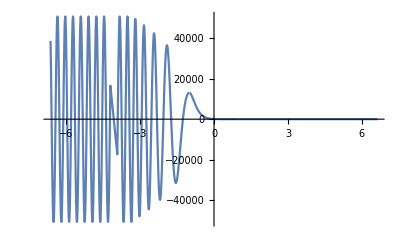

-0.541062

```mathematica
(*TM-wave*)
step=0.00000000001;
Singularity1 =DSolveValue[y''[x]-(2a/(2*a*x+ⅈ*v))*y'[x]-χ^2*Sin[t]^2*y[x]==0,y,x];
Singularity2 =DSolveValue[y''[x]+(2a/(-2*a*x+ⅈ*v))*y'[x]-χ^2*Sin[t]^2*y[x]==0,y,x];

BTMEquation={y''[x]-(Epsilon'[x]/Epsilon[x])*y'[x]+χ^2*(Epsilon[x]-Sin[t]^2)*y[x]==0};

(*Right and simpliest part*)
BTMInitials1={y[X0]==-A,y'[X0]==-ⅈ*χ*Epsilon[X0]*A*Cos[t]};
BTM1=NDSolveValue[{BTMEquation,BTMInitials1},y,{x,1+step,X0},WorkingPrecision->30,MaxSteps->10^6];

firstPoint={Singularity1[step]==BTM1[1+step],Singularity1'[step]==BTM1'[1+step]};
firstSol=NSolve[firstPoint,{C[1],C[2]}];

(*Middle part*)
BTMInitials2={y[1-step]==Singularity1[-step]/.firstSol,y'[1-step]==Singularity1'[-step]/.firstSol};
BTM2=NDSolveValue[{BTMEquation,BTMInitials2},y,{x,-1+step,1-step},WorkingPrecision->30,MaxSteps->10^6];

secondPoint={Singularity2[step]==BTM2[-1+step],Singularity2'[step]==BTM2'[-1+step]};
secondSol=NSolve[secondPoint,{C[1],C[2]}];

(*Last and most important part*)
BTMInitials3={y[-1-step]==Singularity2[-step]/.secondSol,y'[-1-step]==Singularity2'[-step]/.secondSol};
BTM3=NDSolveValue[{BTMEquation,BTMInitials3},y,{x,-X0,-1-step},WorkingPrecision->30,MaxSteps->10^6];

BTM=Function[x,Piecewise[{{BTM1[x],x>1+step},{BTM2[x],1-step>x>-1+step},{BTM3[x],x<-1-step}}]];
Plot[Re[BTM[x]],{x,-X0,X0},PlotRange->Full]

RTM=Exp[2*ⅈ*χ*(-X0)]*(ⅈ*χ*BTM[-X0]-BTM'[-X0])/(ⅈ*χ*BTM[-X0]+BTM'[-X0]);
TTM=BTM[X0]*Exp[-ⅈ*χ*(X0)]*(Exp[ⅈ*χ*(-X0)]+RTM*Exp[-ⅈ*χ*(-X0)])/BTM[-X0];

TMDissipation=1-Abs[RTM]^2-Abs[TTM]^2
```

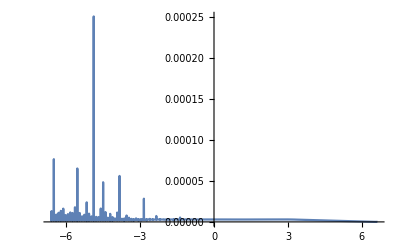

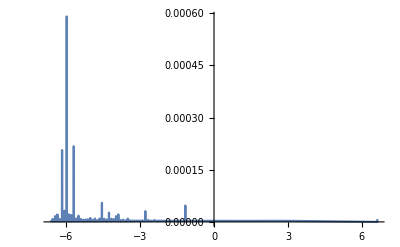

```mathematica
(*Reletive precision*)
ETM=Function[x,Piecewise[{{ⅈ*BTM1'[x]/(χ*Epsilon[x]),x>1+step},{ⅈ*BTM2'[x]/(χ*Epsilon[x]),1-step>x>-1+step},{ⅈ*BTM3'[x]/(χ*Epsilon[x]),x<-1-step}}]];
Plot[Abs[ETE[0][x]-ETM[x]]/Min[Abs[ETE[0][x]],Abs[ETM[x]]],{x,-X0,X0},PlotRange->Full]

BTE=Function[x,(-ⅈ/χ)*ETE[0]'[x]];
Plot[Abs[BTE[x]+BTM[x]]/Min[Abs[BTE[x]],Abs[BTM[x]]],{x,-X0,X0},PlotRange->Full]
```

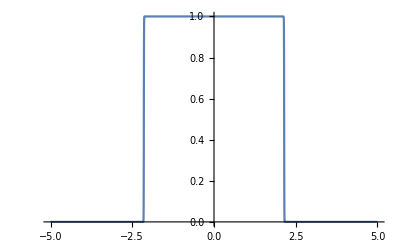

```mathematica
Plot[1/(1+Exp[Exp[x^2]-100]),{x,-5,5}]
```